```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["GiNaC.wl"];
```

RG/GiNaC/bin/G.exe

[info]: 'RG/GiNaC/GiNaC.wl' loaded

```mathematica
points = Range[0,2+1/2,1/6];
points = Union@Flatten[Table[points*Exp[ⅈ i π / 8],{i, 0, 15}]];
```

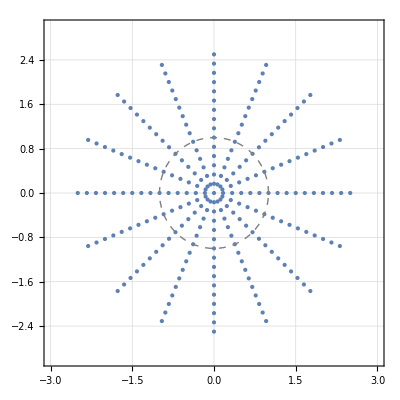

```mathematica
g1=ListPlot[
Evaluate[Through[{Re,Im}[#]]&/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]
```

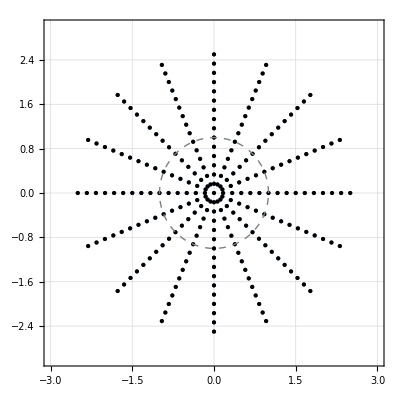
-Graphics-2z:>-21-z-log(1-z) log(z)+π^2/6

```mathematica
Quiet[Block[{i=1},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},With[{expr1=PolyLog[2,z],expr2=ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]])},If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`z_]|Verbatim[RG`GiNaC`Private`z]->z]//TraditionalForm]&
],{N::meprec,Infinity::indet}]
```

```mathematica
Quiet[Block[{i=2},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},
With[{expr1=PolyLog[2,z],expr2=ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]])},
If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`z_]|Verbatim[RG`GiNaC`Private`z]->z]//TraditionalForm]&
],{N::meprec,Infinity::indet,Power::infy}]
```

-Graphics-2z:>-21/z-1/2 log^2(-z)-π^2/6

```mathematica
Quiet[Block[{i=3},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},
With[{expr1=PolyLog[2,z],expr2=ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]])},
If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`z_]|Verbatim[RG`GiNaC`Private`z]->z]//TraditionalForm]&
],{N::meprec,Infinity::indet,Power::infy}]
```

-Graphics-2z:>-2-z/(1-z)-1/2 log^2(1-z)

```mathematica
Quiet[Block[{i=4},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},
With[{expr1=PolyLog[2,z],expr2=ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]])},
If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`z_]|Verbatim[RG`GiNaC`Private`z]->z]//TraditionalForm]&
],{N::meprec,Infinity::indet,Power::infy}]
```

-Graphics-2z:>(2z^2)/2-2-z

```mathematica
Quiet[Block[{i=5},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},
With[{expr1=PolyLog[2,z],expr2=ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]])},
If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`z_]|Verbatim[RG`GiNaC`Private`z]->z]//TraditionalForm]&
],{N::meprec,Infinity::indet,Power::infy}]
```

-Graphics-2z:>-(21-z^2)/2+2z+1-1/2 log(z^2) log(1-z^2)+log(-z) log(z+1)-π^2/12

```mathematica
Quiet[Block[{i=6},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},
With[{expr1=PolyLog[2,z],expr2=ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]])},
If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`x_]|Verbatim[RG`GiNaC`Private`x]->x]//TraditionalForm]&
],{N::meprec,Infinity::indet,Power::infy,LessEqual::nord}]
```

-Graphics-2x/;-1≤x≤1:>2-x+2-(1-x)/(x+1)-2(1-x)/(x+1)+log((x+1)/(1-x)) log(x)+π^2/4

```mathematica
Quiet[Block[{i=7},
ListPlot[
With[{func=Function[{z},Style[{Re[z],Im[z]},
With[{expr1=PolyLog[2,z],expr2=(ReleaseHold@(Hold[PolyLog[2,z]]/.rule`Li2[[i]]))},
If[HoldForm[expr1]=!=HoldForm[expr2]&&Abs[expr1-expr2]<10^-12,Darker@Green,Darker@Red,Darker@Yellow]]]]},func/@points],
AspectRatio->1,
PlotRange->{{-3,3},{-3,3}},
PlotTheme->"Detailed",
PlotStyle->{PointSize[Large]},
Epilog->{Gray,Thin,Dashed,Circle[]}
]//Labeled[#,(rule`Li2[[i]])//ReplaceAll[Verbatim[RG`GiNaC`Private`x_]|Verbatim[RG`GiNaC`Private`x]->x]//TraditionalForm]&
],{N::meprec,Infinity::indet,Power::infy,LessEqual::nord,Greater::nord}]
```

-Graphics-2x/;x>1:>-21/x-1/2 log^2(x)-ⅈ π log(x)+π^2/3